```mathematica
"1.1.3.a.Интерполяционный многочлен Лагранжа (алгебраическое интерполирование)"
```

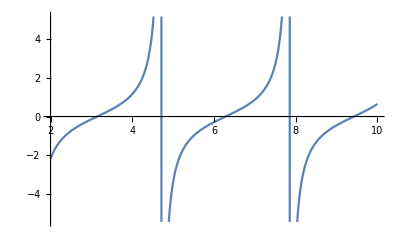

```mathematica
f[x_]:=Tan[x]
Plot[f[q],{q,2,10}]
```

```mathematica
a=-1.5; (*начальное значения икса*)
b=1.5; (*конечное значения икса*)
h=0.25; (*шаг разбиений*)
n=Length@x; (*количество разбиений*)
x=Range[a,b,h]; (*таблица иксов*)
y=Table[f[x[[i]]],{i,1,Length@x}]; (*таблица игриков*)
```

```mathematica
product[z1_,l_]:=Module[{z=z1,i=l,h=1},
For[j=1,j≤Length@x,j++,
If[j==i,h=h,h=h*(z-x[[j]])/(x[[i]]-x[[j]])]];
Return@h]
```

```mathematica
Lagrange[q_]:=Simplify@Sum[product[q,k]*y[[k]],{k,1,Length@x}] (*Интерполяционный многочлен Лагранжа*)
```

```mathematica
Lagrange[v]
```

0.+0.991459 v-8.88178×10^-16 v^2+0.53368 v^3-6.57252×10^-14 v^4-1.03518 v^5-2.91323×10^-13 v^6+2.58163 v^7-6.75016×10^-14 v^8-2.19621 v^9+3.19744×10^-14 v^10+0.682031 v^11-1.33227×10^-15 v^12

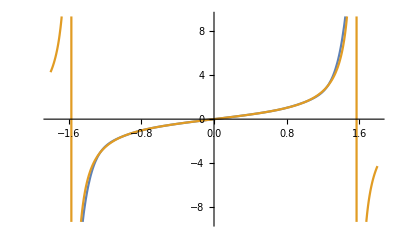

```mathematica
Plot[{Lagrange[v],f[v]},{v,-1.8,1.8}]
```